```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/aj/Documents/3D prints/Ion trap/saddle

```mathematica
ParentDirectory["/home/aj/Documents/3D prints/Ion trap/saddle"]
```

/home/aj/Documents/3D prints/Ion trap

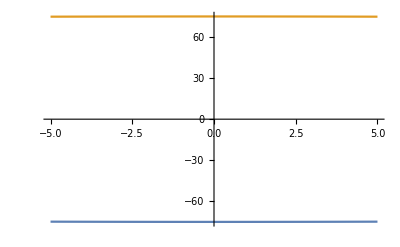

```mathematica
r0 = 150/2;
h0=25/2;
Plot[{-Sqrt[r0^2-x^2],Sqrt[r0^2-x^2]},{x,-5,5}]
```

```mathematica
"Version 1"
Plot3D[h0/r0^2* (x^2 - y^2), {x,-150,150},{y,-150,150},PlotTheme->"ThickSurface"]
```

Version 1

-Graphics3D-

```mathematica
"Version 2 - pingpong size"
r0 = 150/2;
h0=100/2;
Plot3D[h0/r0^2* (x^2 - y^2), {x,-60,60},{y,-60,60},PlotTheme->"ThickSurface"]
```

Version 2 - pingpong size

-Graphics3D-

```mathematica
Export["saddle-theory_v2.stl",%]
```

saddle-theory_v2.stl